Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1+(Om0/Ow0)^(1/3/w)}}

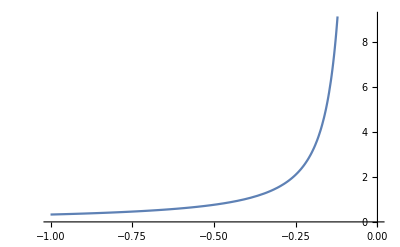

{}

```mathematica
Om0=0.3;
Ow0=0.7;
w=-0.4;
ClearAll["Global`*"]



Om[a_]:=Om0*a^(-3)/(Om0*a^(-3)+Ow0*a^(-3*(1+w)))
Ow[a_]:=Ow0*a^(-3*(1+w))/(Om0*a^(-3)+Ow0*a^(-3*(1+w)))

Solve[Om0==Ow0*(1/(1+x))^(-3*w),x]

equality[w_]:=-1+(Om0/Ow0)^(1/(3w))

Om0=0.3;
Ow0=0.7;
Plot[equality[w],{w,-1,0}]
```